```mathematica
Subscript[L, 1]=1
Subscript[L, 2]=1
```

1

1

```mathematica
hx=Subscript[L, 1]*Cos[Subscript[q, 1]]+Subscript[L, 2]*Cos[Subscript[q, 1]+Subscript[q, 2]]
hy=Subscript[L, 1]*Sin[Subscript[q, 1]]+Subscript[L, 2]*Sin[Subscript[q, 1]+Subscript[q, 2]]

(JJ={{D[hx,Subscript[q, 1]],D[hx,Subscript[q, 2]]},{D[hy,Subscript[q, 1]],D[hy,Subscript[q, 2]]}}) // MatrixForm

(hh={{hx},{hy}}) // MatrixForm
x=1/2*Sin[t]
y=1/2*Cos[t]
(p={{x},{y}}) //MatrixForm

ll=100
F=ll*Inverse[JJ].(p-hh) // Factor
```

Cos[q_1]+Cos[q_1+q_2]

Sin[q_1]+Sin[q_1+q_2]

(-Sin[q_1]-Sin[q_1+q_2] | -Sin[q_1+q_2]
Cos[q_1]+Cos[q_1+q_2] | Cos[q_1+q_2])

(Cos[q_1]+Cos[q_1+q_2]
Sin[q_1]+Sin[q_1+q_2])

Sin[t]/2

Cos[t]/2

(Sin[t]/2
Cos[t]/2)

100

{{(50 (2 Cos[q_1] Cos[q_1+q_2]+2 Cos[q_1+q_2]^2-Cos[q_1+q_2] Sin[t]-Cos[t] Sin[q_1+q_2]+2 Sin[q_1] Sin[q_1+q_2]+2 Sin[q_1+q_2]^2))/(Cos[q_1+q_2] Sin[q_1]-Cos[q_1] Sin[q_1+q_2])},{(50 (2 Cos[q_1]^2+4 Cos[q_1] Cos[q_1+q_2]+2 Cos[q_1+q_2]^2-Cos[q_1] Sin[t]-Cos[q_1+q_2] Sin[t]-Cos[t] Sin[q_1]+2 Sin[q_1]^2-Cos[t] Sin[q_1+q_2]+4 Sin[q_1] Sin[q_1+q_2]+2 Sin[q_1+q_2]^2))/(-Cos[q_1+q_2] Sin[q_1]+Cos[q_1] Sin[q_1+q_2])}}

```mathematica
eq={{Subscript[q, 1]'[t]},{Subscript[q, 2]'[t]}}-(F /. {Subscript[q, 1]->Subscript[q, 1][t],Subscript[q, 2]->Subscript[q, 2][t]})
eeq=Flatten[eq]
```

{{-((50 (2 Cos[q_1[t]] Cos[q_1[t]+q_2[t]]+2 Cos[q_1[t]+q_2[t]]^2-Cos[q_1[t]+q_2[t]] Sin[t]-Cos[t] Sin[q_1[t]+q_2[t]]+2 Sin[q_1[t]] Sin[q_1[t]+q_2[t]]+2 Sin[q_1[t]+q_2[t]]^2))/(Cos[q_1[t]+q_2[t]] Sin[q_1[t]]-Cos[q_1[t]] Sin[q_1[t]+q_2[t]]))+q_1'[t]},{-((50 (2 Cos[q_1[t]]^2+4 Cos[q_1[t]] Cos[q_1[t]+q_2[t]]+2 Cos[q_1[t]+q_2[t]]^2-Cos[q_1[t]] Sin[t]-Cos[q_1[t]+q_2[t]] Sin[t]-Cos[t] Sin[q_1[t]]+2 Sin[q_1[t]]^2-Cos[t] Sin[q_1[t]+q_2[t]]+4 Sin[q_1[t]] Sin[q_1[t]+q_2[t]]+2 Sin[q_1[t]+q_2[t]]^2))/(-Cos[q_1[t]+q_2[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_1[t]+q_2[t]]))+q_2'[t]}}

{-((50 (2 Cos[q_1[t]] Cos[q_1[t]+q_2[t]]+2 Cos[q_1[t]+q_2[t]]^2-Cos[q_1[t]+q_2[t]] Sin[t]-Cos[t] Sin[q_1[t]+q_2[t]]+2 Sin[q_1[t]] Sin[q_1[t]+q_2[t]]+2 Sin[q_1[t]+q_2[t]]^2))/(Cos[q_1[t]+q_2[t]] Sin[q_1[t]]-Cos[q_1[t]] Sin[q_1[t]+q_2[t]]))+q_1'[t],-((50 (2 Cos[q_1[t]]^2+4 Cos[q_1[t]] Cos[q_1[t]+q_2[t]]+2 Cos[q_1[t]+q_2[t]]^2-Cos[q_1[t]] Sin[t]-Cos[q_1[t]+q_2[t]] Sin[t]-Cos[t] Sin[q_1[t]]+2 Sin[q_1[t]]^2-Cos[t] Sin[q_1[t]+q_2[t]]+4 Sin[q_1[t]] Sin[q_1[t]+q_2[t]]+2 Sin[q_1[t]+q_2[t]]^2))/(-Cos[q_1[t]+q_2[t]] Sin[q_1[t]]+Cos[q_1[t]] Sin[q_1[t]+q_2[t]]))+q_2'[t]}

```mathematica
tf=10;
sol=NDSolve[{eeq[[1]]==0,eeq[[2]]==0,Subscript[q, 1][0]==1,Subscript[q, 2][0]==1},{Subscript[q, 1][t],Subscript[q, 2][t]},{t,0,tf}]
```

{{q_1[t]→InterpolatingFunction[…][t],q_2[t]→InterpolatingFunction[…][t]}}

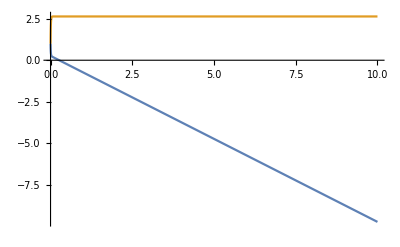

```mathematica
Plot[Evaluate[{Subscript[q, 1][t],Subscript[q, 2][t]}/. sol ],{t,0,tf},PlotRange->All]
```

Cos[q_1[t]]+Cos[q_1[t]+q_2[t]]

Sin[q_1[t]]+Sin[q_1[t]+q_2[t]]

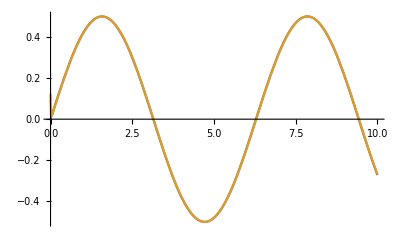

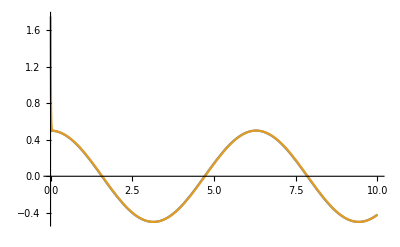

```mathematica
hxt=hx /. {Subscript[q, 1]->Subscript[q, 1][t],Subscript[q, 2]->Subscript[q, 2][t]}
hyt=hy /. {Subscript[q, 1]->Subscript[q, 1][t],Subscript[q, 2]->Subscript[q, 2][t]}
Plot[Evaluate[{x,hxt}/. sol],{t,0,tf},PlotRange->All]
Plot[Evaluate[{y,hyt}/. sol],{t,0,tf},PlotRange->All]
```

```mathematica
InversaTD[{qq1_,qq2_}]:=Module[{hx,hy,JJ,hh,x,y,p,ll,F,q1,q2,T,L1,L2},
T=0.01;
L1=1;
L2=1;
hx=L1*Cos[q1]+L2*Cos[q1+q2];
hy=L1*Sin[q1]+L2*Sin[q1+q2];

JJ={{D[hx,q1],D[hx,q2]},{D[hy,q1],D[hy,q2]}} ;

hh={{hx},{hy}} ;
x=1/2;
y=1/2;
p={{x},{y}} ;

ll=1;
F={{q1},{q2}}+T*ll*Inverse[JJ].(p-hh) /. {q1->qq1,q2->qq2} ;
Flatten[F]
]
```

```mathematica
InversaTD[{1,1}]
```

{0.984625,1.02547}

{1,1}

1000

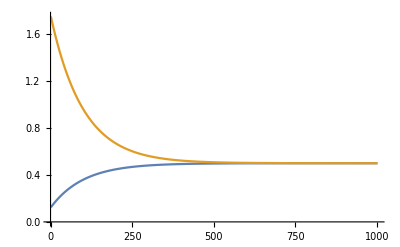

```mathematica
Subscript[s, 0]={1,1}
nn=1000
Do[Subscript[s, i]=InversaTD[Subscript[s, i-1]],{i,1,nn}]
L1=Table[Subscript[s, i][[1]],{i,0,nn}];
L2=Table[Subscript[s, i][[2]],{i,0,nn}];
K1=Cos[L1]+Cos[L1+L2];
K2=Sin[L1]+Sin[L1+L2];
ListLinePlot[{K1,K2},PlotRange->All]
```